# Cosmology Calculator

```mathematica
Clear["Global`*"];
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

-Graphics-

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

Friedmann equation: (FROM https://en.wikipedia.org/wiki/Hubble%27s_law)

-Graphics-

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

```mathematica
(*(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrimePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],z]*D[1/a-1,a]*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d ^2HH)/dtau^2 = dH/dz  dz/da da/dtau*)*)
```

The equation to find a’’(\tau) which must be consistent with what we find previously. We don’t need to do it, instead we can just

-Graphics-

-Graphics-

Here we neglect pressure from radiation, meaning that we don' t go deep to the radiation domination and we start our equations from z = 1000 for example

```mathematica
(*Here we neglect pressure from radiation, meaning that we don't go deep to the radiation domination and we start our equations from z=1000 for example*)

dNlnH[NN_,H0_,Ωm_,Ωd_,w_]:= D[ Log[ConformalHubble[1/E^NN-1,H0,Ωm,Ωd,w,0]],NN](*N=ln a*)
Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN])+dNlnH[NN,H0,Ωm,Ωd,w])ψ[NN]
(*Psiequation[ψ_,N_,H0_,Ωm_,Ωd_,w_,Ωr_]:= ψ''[N] +(3+ dNlnH[N,H0,Ωm,Ωd,w,Ωr])ψ'[N]+(2-(3 Ωm)/(2 Ωm + 2(1-Ωm)Exp[-3w N])+dNlnH[N,H0,Ωm,Ωd,w,Ωr])ψ[N]*)
(*Eq =ψ''[lna] +(3+dlnHdlna)ψ'[lna]+(2-(3Ωm)/(2Ωm + 2(1-Ωm)Exp[-3w lna])+dlnHdlna)ψ[lna]== 0*)
(*dlnHdlna = -(Ωm + (1+3w)(1-Ωm)Exp[-3w lna])/(2Ωm + 2(1-Ωm)Exp[-3w lna]);
DSolve[(ψ''[lna] +(3+dlnHdlna)ψ'[lna]+(2-(3Ωm)/(2Ωm + 2(1-Ωm)Exp[-3w lna])+dlnHdlna)ψ[lna]== 0),ψ[lna], lna]*)
```

```mathematica
(*Psiequation[ψ,NN,H0,Ωm,Ωd,w,Ωr]==0*)
(*s = NDSolve[{((a'[tau] -a[tau]H0 √(Ωm a[tau]^-1+(1-Ωm)a[tau]^(-(1+3 w)))== 0)/.Ωm-> 3/10/.w->-0.9/.H0-> 0.7),a[45]==1},a[tau], {tau,0.001,45}]*)
```

RESULTS

τ :  with high accuracy

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;
NumberForm[tau[0,H0,Ωm,Ωd,w,Ωr],12]
```

46.333381797

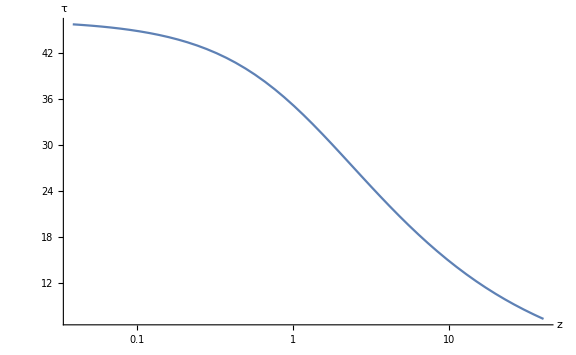

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;
LogLinearPlot[tau[z,H0,Ωm,Ωd,w,Ωr],{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for \HH(z)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

H0 √(Ωd (z+1)^(3 w+1)+Ωm (z+1)+Ωr (z+1)^2)

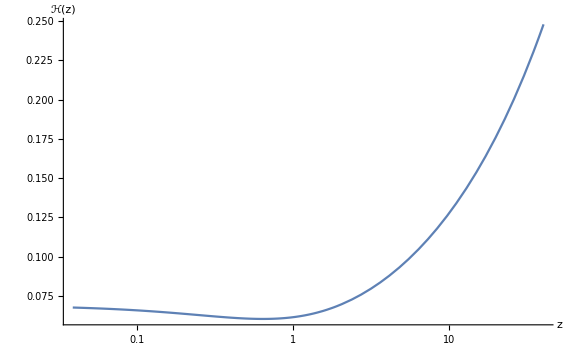

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for d \HH/dtau (z)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

-1/2 H0^2 (z+1) ((3 w+1) Ωd (z+1)^(3 w)+Ωm+2 Ωr (z+1))

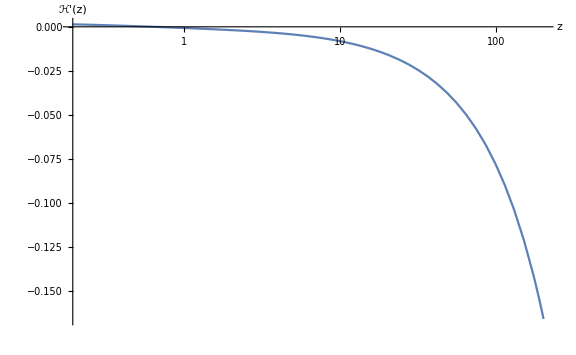

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,200},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ'(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for Ψ

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Sol = DSolve[(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0),ψ[NN], NN];
Print[Sol];
```

{{ψ[NN]→C[1] Hypergeometric2F1[1/2-1/(2 w),-1/(3 w),1-5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]+((ⅇ^-NN)^(3 w))^(5/6/w) Ωd^(5/6/w) Ωm^(-5/6/w) C[2] Hypergeometric2F1[1/2+1/(3 w),1/(2 w),1+5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]}}

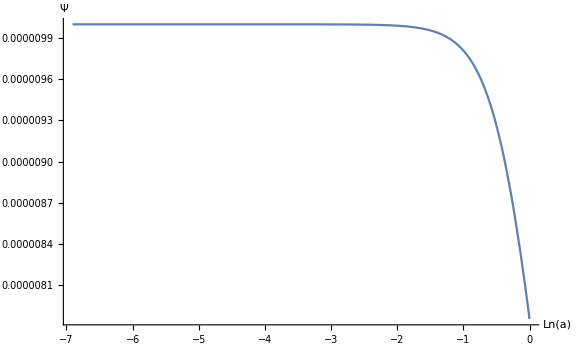

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Plot[ψ[NN]/.Sol/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1/.C[1]->10^-5/.C[2]->0,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

Numerical solution of Ψ

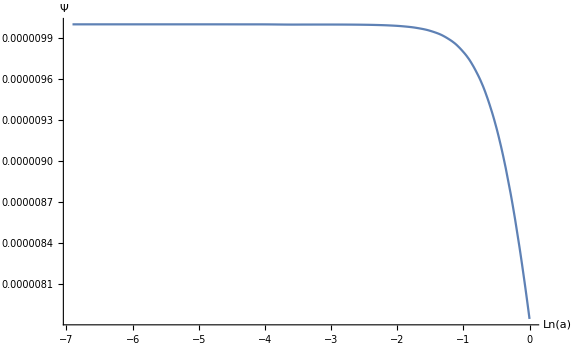

```mathematica
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0)/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]}];
Plot[ψ[NN]/.Solnumer,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```